```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];


e1=Take[Import[wd<>"/../../output/e_1.000.dat"]][[All,{1,2,4}]];
e2=Take[Import[wd<>"/../../output/e_1.500.dat"]][[All,{1,2,4}]];
e3=Take[Import[wd<>"/../../output/e_2.000.dat"]][[All,{1,2,4}]];
e4=Take[Import[wd<>"/../../output/e_2.500.dat"]][[All,{1,2,4}]];
e5=Take[Import[wd<>"/../../output/e_3.000.dat"]][[All,{1,2,4}]];
e6=Take[Import[wd<>"/../../output/e_3.500.dat"]][[All,{1,2,4}]];

plpt1=Take[Import[wd<>"/../../output/plpt_1.000.dat"]][[All,{1,2,4}]];
plpt2=Take[Import[wd<>"/../../output/plpt_1.500.dat"]][[All,{1,2,4}]];
plpt3=Take[Import[wd<>"/../../output/plpt_2.000.dat"]][[All,{1,2,4}]];
plpt4=Take[Import[wd<>"/../../output/plpt_2.500.dat"]][[All,{1,2,4}]];
plpt5=Take[Import[wd<>"/../../output/plpt_3.000.dat"]][[All,{1,2,4}]];
plpt6=Take[Import[wd<>"/../../output/plpt_3.500.dat"]][[All,{1,2,4}]];

ux1=Take[Import[wd<>"/../../output/ux_1.000.dat"]][[All,{1,2,4}]];
ux2=Take[Import[wd<>"/../../output/ux_1.500.dat"]][[All,{1,2,4}]];
ux3=Take[Import[wd<>"/../../output/ux_2.000.dat"]][[All,{1,2,4}]];
ux4=Take[Import[wd<>"/../../output/ux_2.500.dat"]][[All,{1,2,4}]];
ux5=Take[Import[wd<>"/../../output/ux_3.000.dat"]][[All,{1,2,4}]];
ux6=Take[Import[wd<>"/../../output/ux_3.500.dat"]][[All,{1,2,4}]];

ur1=Take[Import[wd<>"/../../output/ur_1.000.dat"]][[All,{1,2,4}]];
ur2=Take[Import[wd<>"/../../output/ur_1.500.dat"]][[All,{1,2,4}]];
ur3=Take[Import[wd<>"/../../output/ur_2.000.dat"]][[All,{1,2,4}]];
ur4=Take[Import[wd<>"/../../output/ur_2.500.dat"]][[All,{1,2,4}]];
ur5=Take[Import[wd<>"/../../output/ur_3.000.dat"]][[All,{1,2,4}]];
ur6=Take[Import[wd<>"/../../output/ur_3.500.dat"]][[All,{1,2,4}]];

aL1=Take[Import[wd<>"/../../output/aL_1.000.dat"]][[All,{1,2,4}]];
aL2=Take[Import[wd<>"/../../output/aL_1.500.dat"]][[All,{1,2,4}]];
aL3=Take[Import[wd<>"/../../output/aL_2.000.dat"]][[All,{1,2,4}]];
aL4=Take[Import[wd<>"/../../output/aL_2.500.dat"]][[All,{1,2,4}]];
aL5=Take[Import[wd<>"/../../output/aL_3.000.dat"]][[All,{1,2,4}]];
aL6=Take[Import[wd<>"/../../output/aL_3.500.dat"]][[All,{1,2,4}]];
```

```mathematica
(*max = 6.0001;*)
max=4.0;

dx= 0.05;
xpts=201;
ypts=201;
zpts=11;

(* i+nx*(j+ny*k) *)
s1=1 + xpts * ((ypts-1)/2 + ypts*(zpts-1)/2)
s2=s1+xpts-1

(*s1=1+xpts*(xpts-1)/2;
s2=xpts*(1+(xpts-1)/2);*)

e6slice=e6[[s1;;s2]]
```

222106

222306

{{-5.,0.,0.0285437},{-4.95,0.,0.0321874},{-4.9,0.,0.0344431},{-4.85,0.,0.0373099},{-4.8,0.,0.0403435},{-4.75,0.,0.0436818},{-4.7,0.,0.0473215},{-4.65,0.,0.0512968},{-4.6,0.,0.0556341},{-4.55,0.,0.0603631},{-4.5,0.,0.065513},{-4.45,0.,0.0711126},{-4.4,0.,0.0771891},{-4.35,0.,0.0837665},{-4.3,0.,0.0908622},{-4.25,0.,0.0984838},{-4.2,0.,0.106624},{-4.15,0.,0.115259},{-4.1,0.,0.124347},{-4.05,0.,0.133827},{-4.,0.,0.143625},{-3.95,0.,0.153652},{-3.9,0.,0.163801},{-3.85,0.,0.173934},{-3.8,0.,0.183824},{-3.75,0.,0.193106},{-3.7,0.,0.201317},{-3.65,0.,0.20815},{-3.6,0.,0.213858},{-3.55,0.,0.219385},{-3.5,0.,0.225647},{-3.45,0.,0.228994},{-3.4,0.,0.229291},{-3.35,0.,0.231004},{-3.3,0.,0.230918},{-3.25,0.,0.227512},{-3.2,0.,0.222798},{-3.15,0.,0.217589},{-3.1,0.,0.211939},{-3.05,0.,0.205855},{-3.,0.,0.199358},{-2.95,0.,0.192512},{-2.9,0.,0.185414},{-2.85,0.,0.178176},{-2.8,0.,0.170908},{-2.75,0.,0.163703},{-2.7,0.,0.156651},{-2.65,0.,0.149806},{-2.6,0.,0.143205},{-2.55,0.,0.136869},{-2.5,0.,0.130812},{-2.45,0.,0.125045},{-2.4,0.,0.119573},{-2.35,0.,0.114395},{-2.3,0.,0.109506},{-2.25,0.,0.104898},{-2.2,0.,0.100562},{-2.15,0.,0.0964867},{-2.1,0.,0.0926609},{-2.05,0.,0.0890722},{-2.,0.,0.0857086},{-1.95,0.,0.0825584},{-1.9,0.,0.0796103},{-1.85,0.,0.076853},{-1.8,0.,0.0742752},{-1.75,0.,0.0718655},{-1.7,0.,0.0696123},{-1.65,0.,0.0675041},{-1.6,0.,0.0655301},{-1.55,0.,0.0636806},{-1.5,0.,0.0619475},{-1.45,0.,0.060324},{-1.4,0.,0.0588044},{-1.35,0.,0.0573834},{-1.3,0.,0.0560558},{-1.25,0.,0.0548158},{-1.2,0.,0.0536571},{-1.15,0.,0.0525738},{-1.1,0.,0.0515603},{-1.05,0.,0.0506122},{-1.,0.,0.0497263},{-0.95,0.,0.0489006},{-0.9,0.,0.0481332},{-0.85,0.,0.0474224},{-0.8,0.,0.0467658},{-0.75,0.,0.0461607},{-0.7,0.,0.0456037},{-0.65,0.,0.0450921},{-0.6,0.,0.0446236},{-0.55,0.,0.0441965},{-0.5,0.,0.0438101},{-0.45,0.,0.0434636},{-0.4,0.,0.043157},{-0.35,0.,0.0428889},{-0.3,0.,0.0426598},{-0.25,0.,0.0424666},{-0.2,0.,0.0423113},{-0.15,0.,0.0421894},{-0.1,0.,0.0421026},{-0.05,0.,0.0420591},{0.,0.,0.0419912},{0.05,0.,0.0420591},{0.1,0.,0.0421026},{0.15,0.,0.0421894},{0.2,0.,0.0423113},{0.25,0.,0.0424666},{0.3,0.,0.0426598},{0.35,0.,0.0428889},{0.4,0.,0.043157},{0.45,0.,0.0434636},{0.5,0.,0.0438101},{0.55,0.,0.0441965},{0.6,0.,0.0446236},{0.65,0.,0.0450921},{0.7,0.,0.0456037},{0.75,0.,0.0461607},{0.8,0.,0.0467658},{0.85,0.,0.0474224},{0.9,0.,0.0481332},{0.95,0.,0.0489006},{1.,0.,0.0497263},{1.05,0.,0.0506122},{1.1,0.,0.0515603},{1.15,0.,0.0525738},{1.2,0.,0.0536571},{1.25,0.,0.0548158},{1.3,0.,0.0560558},{1.35,0.,0.0573834},{1.4,0.,0.0588044},{1.45,0.,0.060324},{1.5,0.,0.0619475},{1.55,0.,0.0636806},{1.6,0.,0.0655301},{1.65,0.,0.0675041},{1.7,0.,0.0696123},{1.75,0.,0.0718655},{1.8,0.,0.0742752},{1.85,0.,0.076853},{1.9,0.,0.0796103},{1.95,0.,0.0825584},{2.,0.,0.0857086},{2.05,0.,0.0890722},{2.1,0.,0.0926609},{2.15,0.,0.0964867},{2.2,0.,0.100562},{2.25,0.,0.104898},{2.3,0.,0.109506},{2.35,0.,0.114395},{2.4,0.,0.119573},{2.45,0.,0.125045},{2.5,0.,0.130812},{2.55,0.,0.136869},{2.6,0.,0.143205},{2.65,0.,0.149806},{2.7,0.,0.156651},{2.75,0.,0.163703},{2.8,0.,0.170908},{2.85,0.,0.178176},{2.9,0.,0.185414},{2.95,0.,0.192512},{3.,0.,0.199358},{3.05,0.,0.205855},{3.1,0.,0.211939},{3.15,0.,0.217589},{3.2,0.,0.222798},{3.25,0.,0.227512},{3.3,0.,0.230918},{3.35,0.,0.231004},{3.4,0.,0.229291},{3.45,0.,0.228994},{3.5,0.,0.225647},{3.55,0.,0.219385},{3.6,0.,0.213858},{3.65,0.,0.20815},{3.7,0.,0.201317},{3.75,0.,0.193106},{3.8,0.,0.183824},{3.85,0.,0.173934},{3.9,0.,0.163801},{3.95,0.,0.153652},{4.,0.,0.143625},{4.05,0.,0.133827},{4.1,0.,0.124347},{4.15,0.,0.115259},{4.2,0.,0.106624},{4.25,0.,0.0984838},{4.3,0.,0.0908622},{4.35,0.,0.0837665},{4.4,0.,0.0771891},{4.45,0.,0.0711126},{4.5,0.,0.065513},{4.55,0.,0.0603631},{4.6,0.,0.0556341},{4.65,0.,0.0512968},{4.7,0.,0.0473215},{4.75,0.,0.0436818},{4.8,0.,0.0403435},{4.85,0.,0.0373099},{4.9,0.,0.0344431},{4.95,0.,0.0321874},{5.,0.,0.0285437}}

```mathematica
pts=1/dx

DarkBlueBlueBlend=Table[Blend[{Darker[Blue],Blue},dx*i],{i,0,pts-1}];
BlueCyanBlend=Table[Blend[{Blue,Cyan},dx*i],{i,0,pts-1}];
CyanGreenBlend=Table[Blend[{Cyan,Green},dx*i],{i,0,pts-1}];
GreenYellowBlend=Table[Blend[{Green,Yellow},dx*i],{i,0,pts-1}];
YellowOrangeBlend=Table[Blend[{Yellow,Orange},dx*i],{i,0,pts-1}];
OrangeRedBlend=Table[Blend[{Orange,Red},dx*i],{i,0,pts-1}];
RedDarkRedBlend=Table[Blend[{Red,Darker[Red]},dx*i],{i,0,pts}];

colors=Flatten[{DarkBlueBlueBlend, BlueCyanBlend, CyanGreenBlend, GreenYellowBlend, YellowOrangeBlend, OrangeRedBlend,RedDarkRedBlend}];

colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Energy"]=Function[x,Blend[Transpose[{colorpts,colors}],x ]];
ColorData["Flow"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

BarLegend[{ColorData["Energy"],{0,1}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]
```

20.

BarLegend[{Function[x,Blend[Transpose[{colorpts,colors}],x]],{0,1}},LegendMarkerSize→300,LabelStyle→{FontSize→13,FontFamily→Arial,GrayLevel[0]}]

BarLegend[{Function[x,Blend[Transpose[{colorpts,colors}],x/max]],{0,4.}},LegendMarkerSize→300,LabelStyle→{FontSize→13,FontFamily→Arial,GrayLevel[0]}]

```mathematica
emax=Max[e1[[1;;All,3]]];

(* Gubser solution *)
q=1.0;
κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*Abs[r])/(1.0+q^2*(τ^2+r^2))];
ux[τ_,r_]:=Sinh[κ[τ,r]]*Sign[r];


e1test=Take[Import[wd<>"/gubser_data/e_1.000.dat"]];
e2test=Take[Import[wd<>"/gubser_data/e_1.500.dat"]];
e3test=Take[Import[wd<>"/gubser_data/e_2.000.dat"]];
e4test=Take[Import[wd<>"/gubser_data/e_2.500.dat"]];
e5test=Take[Import[wd<>"/gubser_data/e_3.000.dat"]];
e6test=Take[Import[wd<>"/gubser_data/e_3.500.dat"]];

plpt1test=Take[Import[wd<>"/gubser_data/plpt_1.000.dat"]];
plpt2test=Take[Import[wd<>"/gubser_data/plpt_1.500.dat"]];
plpt3test=Take[Import[wd<>"/gubser_data/plpt_2.000.dat"]];
plpt4test=Take[Import[wd<>"/gubser_data/plpt_2.500.dat"]];
plpt5test=Take[Import[wd<>"/gubser_data/plpt_3.000.dat"]];
plpt6test=Take[Import[wd<>"/gubser_data/plpt_3.500.dat"]];

aL1test=Take[Import[wd<>"/gubser_data/aL_1.000.dat"]];
aL2test=Take[Import[wd<>"/gubser_data/aL_1.500.dat"]];
aL3test=Take[Import[wd<>"/gubser_data/aL_2.000.dat"]];
aL4test=Take[Import[wd<>"/gubser_data/aL_2.500.dat"]];
aL5test=Take[Import[wd<>"/gubser_data/aL_3.000.dat"]];
aL6test=Take[Import[wd<>"/gubser_data/aL_3.500.dat"]];

ux1test=Table[{-5.0 +i*dx,ux[1.0,-5.0+i*dx]},{i,0,xpts-1}];
ux2test=Table[{-5.0 +i*dx,ux[1.5,-5.0+i*dx]},{i,0,xpts-1}];
ux3test=Table[{-5.0 +i*dx,ux[2.0,-5.0+i*dx]},{i,0,xpts-1}];
ux4test=Table[{-5.0 +i*dx,ux[2.5,-5.0+i*dx]},{i,0,xpts-1}];
ux5test=Table[{-5.0 +i*dx,ux[3.0,-5.0+i*dx]},{i,0,xpts-1}];
ux6test=Table[{-5.0 +i*dx,ux[3.5,-5.0+i*dx]},{i,0,xpts-1}];



(*****************************************)


e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
e4slice=e4[[s1;;s2,{1,3}]];
e5slice=e5[[s1;;s2,{1,3}]];
e6slice=e6[[s1;;s2,{1,3}]];

plpt1slice=plpt1[[s1;;s2,{1,3}]];
plpt2slice=plpt2[[s1;;s2,{1,3}]];
plpt3slice=plpt3[[s1;;s2,{1,3}]];
plpt4slice=plpt4[[s1;;s2,{1,3}]];
plpt5slice=plpt5[[s1;;s2,{1,3}]];
plpt6slice=plpt6[[s1;;s2,{1,3}]];


ux1slice=ux1[[s1;;s2,{1,3}]];
ux2slice=ux2[[s1;;s2,{1,3}]];
ux3slice=ux3[[s1;;s2,{1,3}]];
ux4slice=ux4[[s1;;s2,{1,3}]];
ux5slice=ux5[[s1;;s2,{1,3}]];
ux6slice=ux6[[s1;;s2,{1,3}]];

aL1slice=aL1[[s1;;s2,{1,3}]];
aL2slice=aL2[[s1;;s2,{1,3}]];
aL3slice=aL3[[s1;;s2,{1,3}]];
aL4slice=aL4[[s1;;s2,{1,3}]];
aL5slice=aL5[[s1;;s2,{1,3}]];
aL6slice=aL6[[s1;;s2,{1,3}]];


magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[2],Opacity[0.3]};
redTran={Red,AbsoluteThickness[2],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[2],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
purplpteTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[2],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,8}],AbsoluteThickness[2]};
purplpte={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,8}],AbsoluteThickness[2]};

style={magentaTran,redTran,orangeTran,greenTran,cyanTran,blueTran,magenta,red,orange,green,cyan, blue};
```

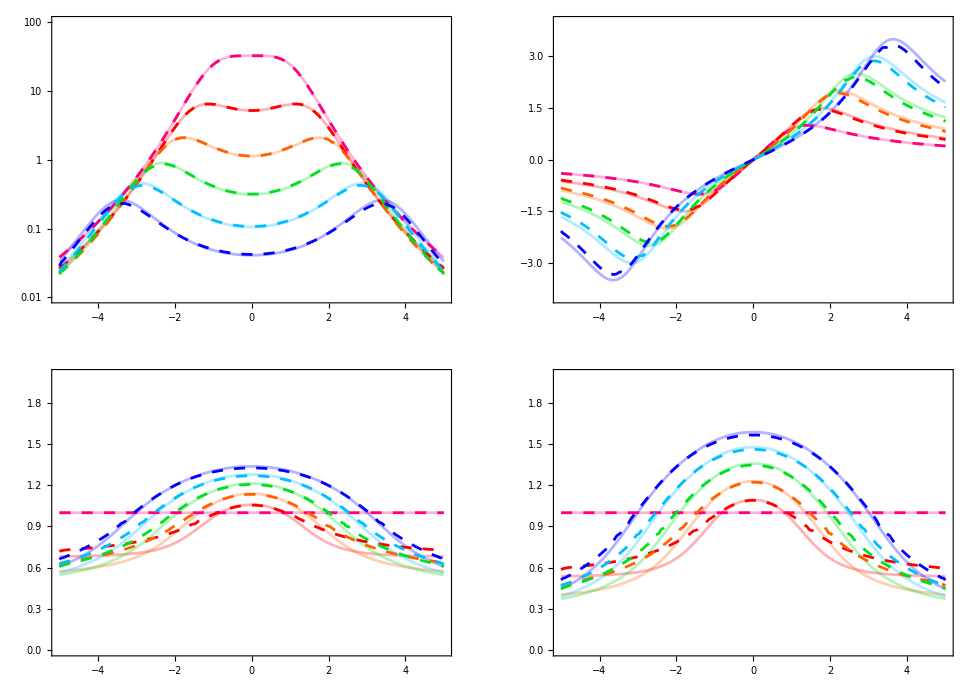

```mathematica
GraphicsGrid[{{
ListLogPlot[{e1test,e2test,e3test,e4test,e5test,e6test,e1slice,e2slice,e3slice,e4slice,e5slice,e6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.01,100}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{ux1test,ux2test,ux3test,ux4test,ux5test,ux6test,ux1slice,ux2slice,ux3slice,ux4slice,ux5slice,ux6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{-4,4}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]},

{ListPlot[{aL1test,aL2test,aL3test,aL4test,aL5test,aL6test,aL1slice,aL2slice,aL3slice,aL4slice,aL5slice,aL6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.,2}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450],

ListPlot[{plpt1test,plpt2test,plpt3test,plpt4test,plpt5test,plpt6test,plpt1slice,plpt2slice,plpt3slice,plpt4slice,plpt5slice,plpt6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.,2.0}},PlotStyle->style,Frame->True,FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->450]}}]

Export[wd<>"/gubser_usual_test.pdf",%];
```

```mathematica
(* PL Matching *)
```

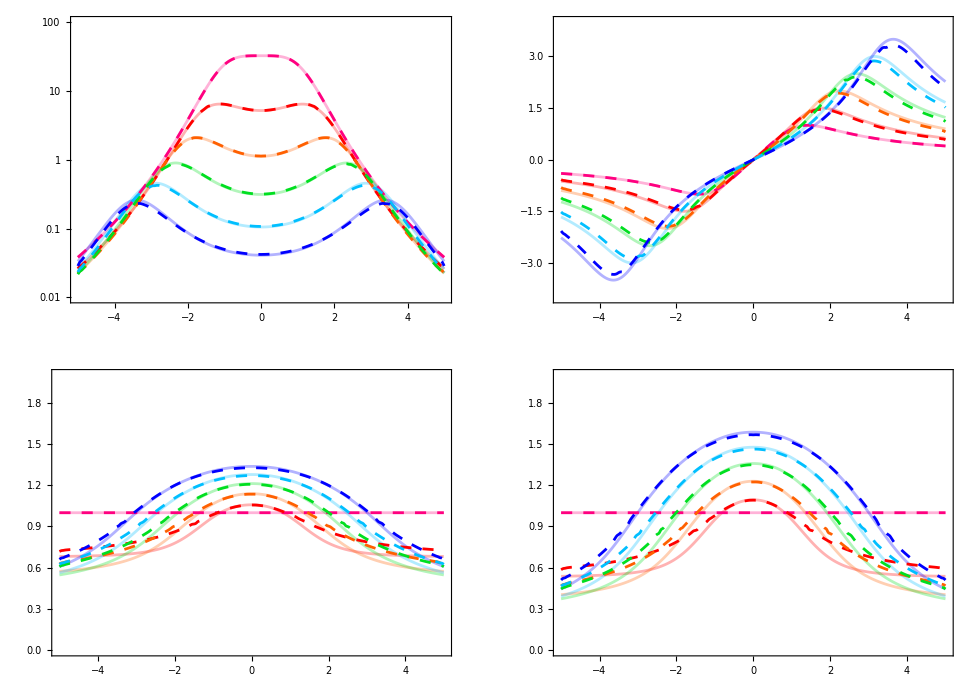
```mathematica
-Graphics-;
```

```mathematica
Max[e1[[All,3]]]
Max[e2[[All,3]]]
Max[e3[[All,3]]]
Max[e4[[All,3]]]
Max[e5[[All,3]]]
Max[e6[[All,3]]]
```

32.4039

6.49831

2.10207

0.935214

0.474638

0.253712

```mathematica
(*plot=Grid[{{ListDensityPlot[e1,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e1[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e2[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e3,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e3[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e4[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e5,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e5[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[e6,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,Max[e6[[All,3]]]}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Top],ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->250]},

{ListDensityPlot[ur1,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur2,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur3,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur4,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur5,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250],
ListDensityPlot[ur6,PlotRange->All,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],Bottom],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->250]}}];*)
```

```mathematica
(*Export[wd<>"/gubser_usual_2d.eps",plot];*)
```